```mathematica
u11[r_]=A Sin[k*r];
u1g[r_]=Exp[-ⅈ*k*a]-S Exp[ⅈ*k*r];

u21[r_]=B Sinh[κ*r];
u2g[r_]=Co Exp[-κ*r];
```

```mathematica
A=(Exp[-ⅈ*k*a]-S Exp[ⅈ*k*a])/Sin[k*a];
B=(Co Exp[-κ*a])/Sinh[κ*a];
```

```mathematica
S=Exp[-2ⅈ*k*a]((ζ-β+ⅈ*k*a)/(ζ-β-ⅈ*k*a))(f[k*a]-g-α/(ζ-β+ⅈ*k*a))/(f[k*a]-g-α/(ζ-β-ⅈ*k*a));
Co=Exp[κ*a](-2Exp[-ⅈ*k*a]α*k*a)((f[κ*a]-g)(ζ-β-ⅈ*k*a)-α^2);
```

```mathematica
ζ=k*a*Cot[k*a];
f[x_]=x *Coth[x]+x;
κ=√(λ^2-k^2);
```

```mathematica
β=.5;
g=2;
a=1;
λ=√1;
```

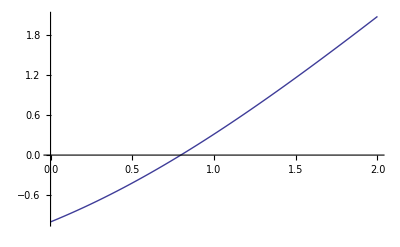

{κs→0.796812}

```mathematica
F=Plot[f[κs*a]-g,{κs,0,2}]
FindRoot[f[κs*a]-g,{κs,0.75}]
```

```mathematica
ζs=ks*a*Cot[ks*a];
κs=0.796812;

ks=√(λ^2-κs^2);
```

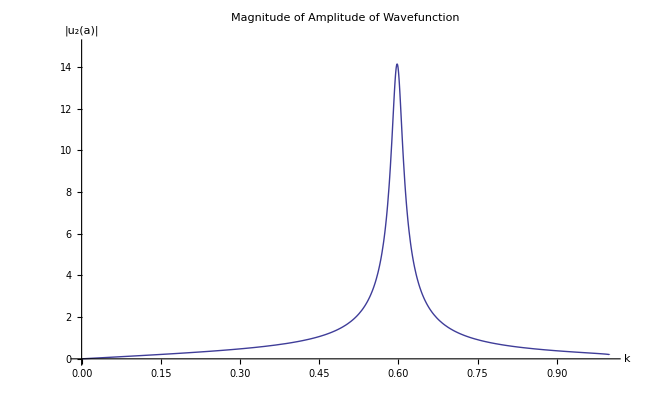

/home/cnewby/SeniorDesign/Final/FBMag.eps

```mathematica
α=.1;

u2[k_]=(2*Abs[α]*k*a)/(√(((ζ-β)(f[κ*a]-g)-α^2)^2+(k*a)^2(f[κ*a]-g)^2));

W1=Plot[u2[k],{k,0,1},PlotRange->{{0,1},{0,15}},PlotLabel->"Magnitude of Amplitude of Wavefunction",AxesLabel->{"k","|u_2(a)|"}]
Export["/home/cnewby/SeniorDesign/Final/FBMag.eps",W1]
```

```mathematica
FindMaximum[u2[k],{k,.61}]
```

{14.1417,{k→0.597586}}

```mathematica
α=.25;
u2[k_]=(2*Abs[α]*k*a)/(√(((ζ-β)(f[κ*a]-g)-α^2)^2+(k*a)^2(f[κ*a]-g)^2));

W2=Plot[u2[k],{k,0,1},PlotRange->{{0,1},{0,15}},PlotStyle->Red];
```

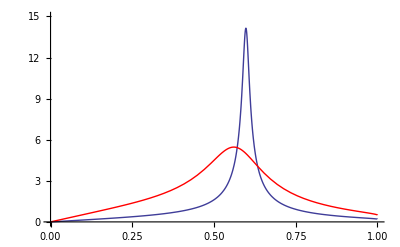

```mathematica
Show[W1,W2]
```

```mathematica
α=0;

Δsp=(-2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));
Γovt=(2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));

ηR=ArcTan[Γovt/(ks^2-k^2)];
η0=(β Sin[k*a]^2)/(k*a);

Q1=Plot[Sin[η0+ηR]^2,{k,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Blue];
```

```mathematica
α=0.1;

Δsp=(-2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));
Γovt=(2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));

ηR=ArcTan[Γovt/(ks^2-k^2)];
η0=(β Sin[k*a]^2)/(k*a);

Q2=Plot[Sin[η0+ηR]^2,{k,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Green];
```

```mathematica
α=0.25;

Δsp=(-2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));
Γovt=(2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));

ηR=ArcTan[Γovt/(ks^2-k^2)];
η0=(β Sin[k*a]^2)/(k*a);

Q3=Plot[Sin[η0+ηR]^2,{k,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Red];
```

```mathematica
α=0.35;

Δsp=(-2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));
Γovt=(2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));

ηR=ArcTan[Γovt/(ks^2-k^2)];
η0=(β Sin[k*a]^2)/(k*a);

Q4=Plot[Sin[η0+ηR]^2,{k,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Orange];
```

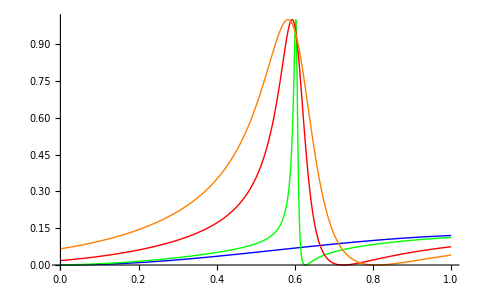

```mathematica
Show[Q1,Q2,Q3,Q4]
```

```mathematica
α=0.15;
β=.001;

Δsp=(-2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));
Γovt=(2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));

ηR=ArcTan[Γovt/(ks^2-k^2)];
η0=(β Sin[k*a]^2)/(k*a);

E1=Plot[Sin[η0+ηR]^2,{k,0,1},PlotRange->{{.4,.8},{0,1}},PlotStyle->Blue];
```

```mathematica
α=0.15;
β=.54;

Δsp=(-2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));
Γovt=(2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));

ηR=ArcTan[Γovt/(ks^2-k^2)];
η0=(β Sin[k*a]^2)/(k*a);

E2=Plot[Sin[η0+ηR]^2,{k,0,1},PlotRange->{{.4,.8},{0,1}},PlotStyle->Green];
```

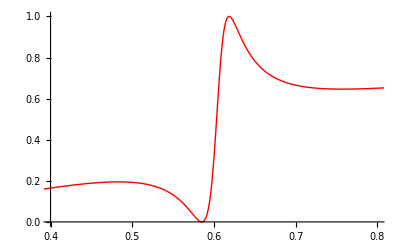

```mathematica
α=0.15;
β=1.35;

Δsp=(-2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));
Γovt=(2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));

ηR=ArcTan[Γovt/(ks^2-k^2)];
η0=(β Sin[k*a]^2)/(k*a);

E3=Plot[Sin[η0+ηR]^2,{k,0,1},PlotRange->{{.4,.8},{0,1}},PlotStyle->Red]
```

```mathematica
α=0.15;
β=-.6;

Δsp=(-2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));
Γovt=(2 α^2(ζs-β)κs*a)/(a^2 f'[κs*a]((ζs-β)^2+(ks*a)^2));

ηR=ArcTan[Γovt/(ks^2-k^2)];
η0=(β Sin[k*a]^2)/(k*a);

E4=Plot[Sin[η0+ηR]^2,{k,0,1},PlotRange->{{.4,.8},{0,1}},PlotStyle->Orange];
```

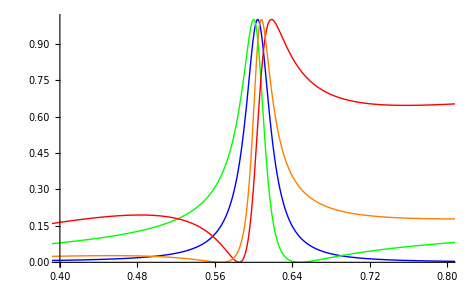

```mathematica
Show[E1,E2,E3,E4]
```